## Two kings and a white rook

```mathematica
(*n=size of the board*)
(*position = {{white king x, white king y}, {black king x, black king y}, {rook x ({-1,-1} if the rook was taken), rook y} 1->white's move; 0->black's move}*)
```

```mathematica
flipVertically[{{w1_,w2_},{b1_,b2_},{-1,-1},m_},n_]:={{n+1-w1,w2},{n+1-b1,b2},{-1,-1},m};
flipVertically[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:={{n+1-w1,w2},{n+1-b1,b2},{n+1-r1,r2},m};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{-1,-1},m_},n_]:={{w1,n+1-w2},{b1,n+1-b2},{-1,-1},m};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:={{w1,n+1-w2},{b1,n+1-b2},{r1,n+1-r2},m};
flipDiagonally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:={{w2,w1},{b2,b1},{r2,r1},m};
toStandardPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=Module[{ans={{w1,w2},{b1,b2},{r1,r2},m}},
If[w1>Ceiling[n/2],ans=flipVertically[ans,n]];
If[ans[[1,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]];
If[ans[[1,1]]>ans[[1,2]],ans=flipDiagonally[ans,n]];
If[ans[[1,1]]==ans[[1,2]]&&ans[[2,2]]>ans[[2,1]],ans=flipDiagonally[ans,n]];
If[OddQ[n]&&ans[[1,2]]==Ceiling[n/2]&&ans[[2,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]];
ans
];(*white king ends up in the eights (w1<n/2, w2<n/2, w1>=w2), 
if the white king is on the main diagonal, then black king ends up in the half (b2>=b1),
if n is odd and w2==Ceiling[n/2], then black king ends up in the half (b2<=n/2)*)
```

```mathematica
kingMoves[x_,y_,n_]:=Module[{possible,legal},
	possible=Table[
		{x+dx,y+dy},
		{dx,-1,1},
		{dy,-1,1}
	];
	possible=Flatten[possible,1];
	legal=DeleteCases[possible,{0|n+1,_}|{_,0|n+1}|{x,y}];
	legal
];(*returns a list of valid moves for a single king*)
```

```mathematica
rookMoves[x_,y_,n_]:=If[x==-1,{},DeleteCases[Join[{#,y}&/@Range[n],{x,#}&/@Range[n]],{x,y}]];(*returns a list of valid moves for a single rook*)
```

```mathematica
validPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=(!(Abs[w1-b1]<=1&&Abs[w2-b2]<=1))&&(((!(w1==r1&&w2==r2))&&(!(b1==r1&&b2==r2))&&(!(m==1&&(r1==b1&&(w1!=b1||w2<Min[b2,r2]||w2>Max[b2,r2]))))&&(!(m==1&&(r2==b2&&(w2!=b2||w1<Min[b1,r1]||w1>Max[b1,r1])))))||r1==-1);
```

```mathematica
nextPositions[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=Module[{ans={}},
If[m==1,(*white's move*)
ans=Join[
{#,{b1,b2},{r1,r2},0}&/@kingMoves[w1,w2,n],
DeleteCases[{{w1,w2},{b1,b2},#,0}&/@rookMoves[r1,r2,n],
p_/;(r1==p[[3,1]]&&w1==r1&&Sign[w2-r2]!=Sign[w2-p[[3,2]]])||
(r2==p[[3,2]]&&w2==r2&&Sign[w1-r1]!=Sign[w1-p[[3,1]]])||
(r1==p[[3,1]]&&b1==r1&&Sign[b2-r2]!=Sign[b2-p[[3,2]]])||
(r2==p[[3,2]]&&b2==r2&&Sign[b1-r1]!=Sign[b1-p[[3,1]]])
]
]
];
If[m==0,(*black's move*)
ans={{w1,w2},#,{r1,r2},1}&/@kingMoves[b1,b2,n];
ans=ans/.{{a_,b_},{c_,d_},{c_,d_},1}->{{a,b},{c,d},{-1,-1},1}
];
ans=DeleteCases[ans,p_/; validPosition[p,n]==False];
DeleteDuplicates[toStandardPosition[#,n]&/@ans]
];
```

```mathematica
edgesFromPosition[p_,n_]:={p->#}&/@nextPositions[p,n];
```

```mathematica
generatePositions[n_]:=DeleteDuplicates[toStandardPosition[#,n]&/@DeleteCases[Join[
Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m},{w1,n},{w2,n},{b1,n},{b2,n},{r1,n},{r2,n},{m,0,1}],6],
Flatten[Table[{{w1,w2},{b1,b2},{-1,-1},m},{w1,n},{w2,n},{b1,n},{b2,n},{m,0,1}],4]
],
p_/; validPosition[p,n]==False
]];(*all possible positions*)
```

```mathematica
isItTerminal[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=Length[nextPositions[{{w1,w2},{b1,b2},{r1,r2},m},n]]==0;
```

```mathematica
isItCheck[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=!validPosition[{{w1,w2},{b1,b2},{r1,r2},1-m},n];
```

```mathematica
isRookCaptured[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_]:=r1==-1;
```

```mathematica
generateInitialPosition[n_]:=Module[{ans={{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},1}},
While[(!validPosition[ans,n])||(isItTerminal[ans,n]),
ans={{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},1}
];
ans
];(*rook is present, it is not mate, not stalemate, and it's white to move*)
```

```mathematica
generateRandomWalkResult[n_]:=With[{cur=generateInitialPosition[n]},
NestWhile[RandomChoice[nextPositions[#,n]]&,cur,(!isItTerminal[#,n])&&(!isRookCaptured[#,n])&]
];
```

```mathematica
generateRandomWalk[n_]:=With[{cur=generateInitialPosition[n]},
NestWhileList[RandomChoice[nextPositions[#,n]]&,cur,(!isItTerminal[#,n])&&(!isRookCaptured[#,n])&]
];
```

```mathematica
generateEdges[positions_,n_]:=Flatten[edgesFromPosition[#,n]&/@positions,2];
```

```mathematica
MakeBoxes[position:ChessPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_},n_],form:StandardForm]:=Module[{table=Table[" ",{i,n},{j,n}],grid},
table[[n-w1+1,w2]]=♔;
table[[n-b1+1,b2]]=♚;
If[r1!=-1,table[[n-r1+1,r2]]=♖];
grid=Grid[table,Dividers->All,ItemSize->{1.,1.},
Background -> {Automatic,Automatic,Flatten[Table[{i, j} -> If[EvenQ[i+j],LightGray, White], {i, n}, {j, n}]]}];
ToBoxes@Interpretation[grid,position]
]
```

```mathematica
ChessPositionData[ChessPosition[data_,n_]]:=data;
```

```mathematica
generateLabels[positions_,n_]:=#->Placed[ChessPosition[#,n],Tooltip]&/@positions;
```

```mathematica
colorFunction[p_,n_]:=If[isRookCaptured[p,n],Blue,(*the rook is captured*)
If[!isItTerminal[p,n],Gray,(*not mate, not stalemate*)
If[isItCheck[p,n],Red,(*mate*)
Yellow(*stalemate*)
]
]
];
```

```mathematica
generateVertexStyle[positions_,n_]:=#->colorFunction[#,n]&/@positions;
```

```mathematica
generateGraph[n_]:=With[{positions=generatePositions[n]},
Graph[generateEdges[positions,n],VertexStyle->generateVertexStyle[positions,n],VertexLabels->generateLabels[positions,n]]
];
```

```mathematica
showWalk[graph_,walk_]:=HighlightGraph[graph,Join[Style[#,Thickness[0.008],Red,Arrowheads[0.05]]&/@Thread[Most[walk]->Rest[walk]](*,Annotation[#,VertexLabels->ChessPosition[#]]&/@{First[walk],Last[walk]}*)]];
```

```mathematica
generateResults[n_,k_]:=Table[generateRandomWalkResult[n],k];
```

```mathematica
generateResultsGraph[n_,k_]:=With[{positions=generatePositions[n]},
Graph[generateEdges[positions,n],VertexStyle->generateVertexStyle[positions,n],VertexLabels->generateLabels[positions,n],VertexSize->Normal[Counts[generateResults[n,k]]*10/k]]
];
```

```mathematica
winningProbability[n_,k_]:=Module[{results=generateResults[n,k]},
Total[If[isItCheck[#,n],1,0]&/@results]/k
];
```

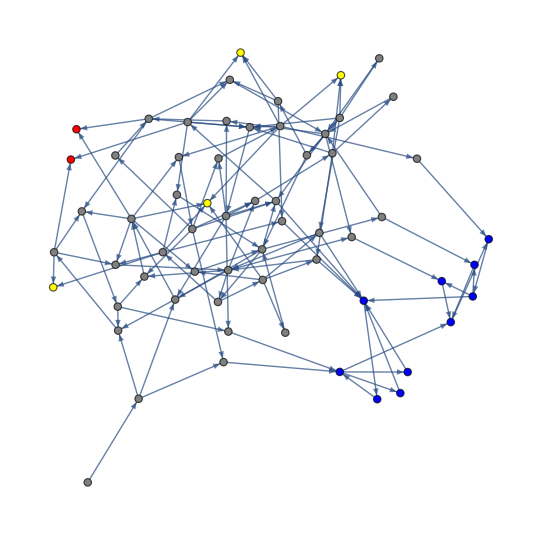

```mathematica
graph=generateGraph[3]
```

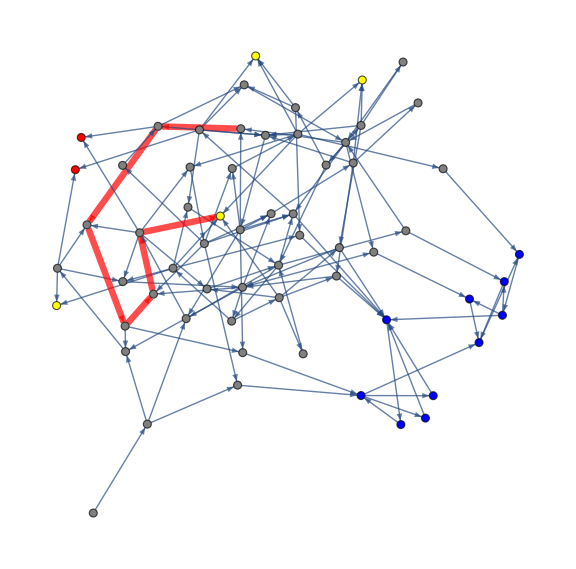

```mathematica
showWalk[graph,generateRandomWalk[3]]
```

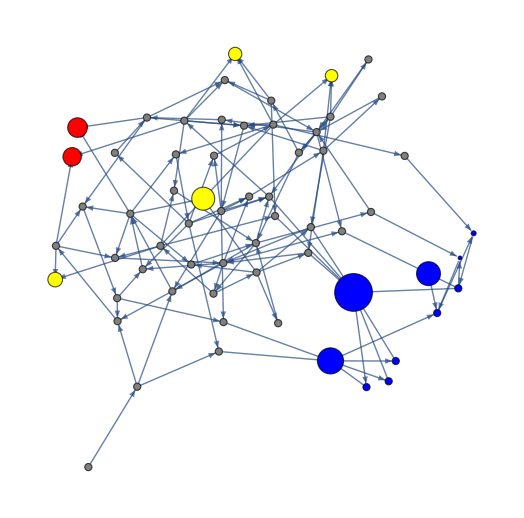

```mathematica
generateResultsGraph[3,1000]
```

{169/1000,69/1000,11/250,7/500,2/125,3/500}

{0.1690.012,0.0690.008,0.0440.006,0.01400.0034,0.0160.004,0.00600.0022}

FittedModel[-0.0241469-0.63484 x]

{-0.0241469-0.63484 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0241469 | 0.402005 | -0.0600661 | 0.954984
x | -0.63484 | 0.0698041 | -9.09459 | 0.000810587}

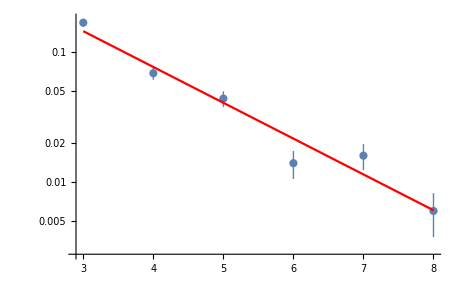

```mathematica
k=1000;
maxSize=8;
eps=10^-6;(*in case of trying to calculate Log[0]*)
winningProbabilities=Table[winningProbability[i,k],{i,3,maxSize}]
probabilitiesWithErrors=MapThread[Around,{winningProbabilities,Sqrt[k winningProbabilities]/k/1.1}](*/1.1 because when the probability is 1/k the errorbar on the plot goes to -inf*)
fit=LinearModelFit[DeleteCases[{Range[3,maxSize],Log[winningProbabilities+eps]},{_,Log[eps]}]//Transpose,{1,x},x]
fit[{"BestFit","ParameterTable"}]
Show[ListLogPlot[{Range[3,maxSize],probabilitiesWithErrors}//Transpose],Plot[Normal@fit,{x,3,maxSize},PlotStyle->Red]]
```